```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Import data thief of WD mass-density + WD mass-radius relations

```mathematica
WD=Import["/Users/NewUser/Documents/Qballs/WD.csv"];
WDrad=Import["/Users/NewUser/Documents/Qballs/WDradius.csv"];
WDreverse=Reverse/@WD;
Massreverse=Interpolation[WDreverse];
WDplot=Interpolation[WD];Radplot=Interpolation[WDrad];
```

```mathematica
PJ[M_]:=0.0126(M/Mch)^(-1/3)(1-(M/Mch)^(4/3))^(1/2)/.Mch->1.456
```

```mathematica
Massreverse[0.5]
```

6.33561

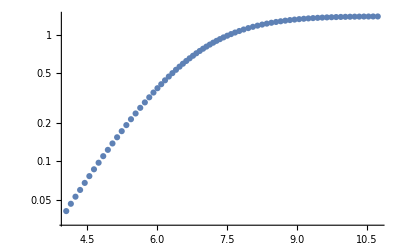

```mathematica
ListLogPlot[WD]
```

```mathematica
Convert[SolarMass/SolarRadius^3,Gram/Centimeter^3]
```

(5.89994 Gram)/Centimeter^3

```mathematica
density[M_]:=If[M<1.2,Log10[M/(4 Pi/3(1/1.1 PJ[M])^3)5.899940315419777]+1,Log10[M/(4 Pi/3(1/1.1 PJ[M])^3)5.899940315419777]+1]
```

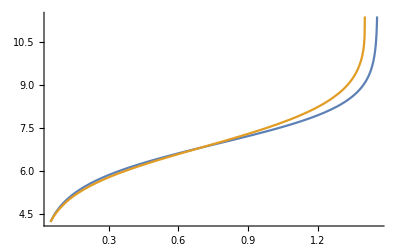

```mathematica
Plot[{density[M],Massreverse[M]},{M,0.05,1.456}]
```

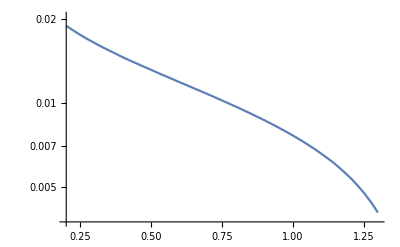

```mathematica
LogPlot[{Radplot[M],radiusfun[M]},{M,0.2,1.3}]
```

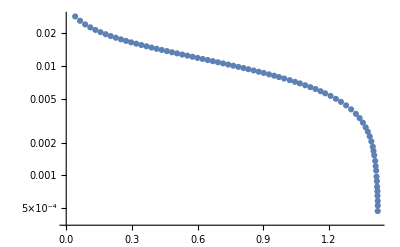

```mathematica
ListLogPlot[WDrad]
```

```mathematica
Convert[PJ[1.25]SolarRadius,Kilo Meter]
```

3958.42 Kilo Meter

```mathematica
Convert[PJ[0.85]SolarRadius,Kilo Meter]
```

7508.6 Kilo Meter

#### V_esc

```mathematica
Clear[vesc]
vesc[M_]:=Convert[Sqrt[2GravitationalConstant*M/Radplot[M]*SolarMass/SolarRadius] 1/SpeedOfLight,d]
```

```mathematica
vesc[1.25]
```

0.0305435

```mathematica
vesc[0.85]
```

0.0182875

#### λ_T as function of mass

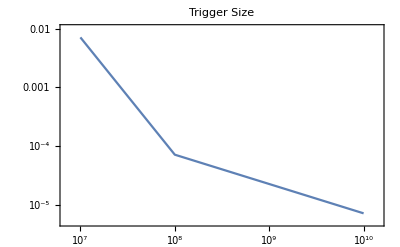

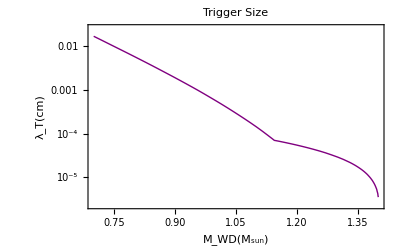

```mathematica
trigger[ρ_]:=If[ρ>10^8,10^-5*(ρ/(5*10^9))^(-1/2),1/(10000 √2)*(ρ/10^8)^-2]
triggermass=Interpolation[Table[{WDplot[logρ],trigger[10^logρ]},{logρ,5,10.6,0.01}]];
LogLogPlot[{trigger[ρ]},{ρ,10^10,10^7},PlotLabel->"Trigger Size",Frame->True]
LogPlot[triggermass[M],{M,0.7,1.4},PlotLabel->"Trigger Size",Frame->True,PlotStyle->{Thick,Purple},FrameLabel->{"M_WD(M_sun)","λ_T(cm)"},FrameStyle->Black]
```

#### E_boom (in GeV) as function of WD mass

```mathematica
triggermass[1.4]
```

3.54314×10^-6

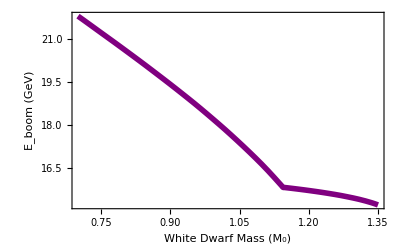

```mathematica
eboom[M_]:=Log10[Convert[(10^Massreverse[M]*Gram/Centimeter^3 SpeedOfLight^2)/(12 Giga ElectronVolt)*4 Pi/3(triggermass[M]Centimeter)^3*(Mega ElectronVolt)1/(Giga ElectronVolt),d]]
eboomreverse[mdm_]:=Interpolation[Table[{eboom[M],M},{M,0.4,1.40,0.01}],InterpolationOrder->1][mdm]
Plot[eboom[M],{M,0.7,1.35},FrameLabel->{"White Dwarf Mass (M_0)","E_boom (GeV)"},Frame->True,FrameStyle->Black,PlotStyle-> {Purple,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```

```mathematica
eboom[1.4]
```

14.5278

```mathematica
eboom[1.25]
```

15.6102

```mathematica
eboom[0.85]
```

20.0373

```mathematica
eboomreverse[15.2]
```

1.35431

#### Model-dependent crust stopping calculation (R_c~ 50 km, (ρ_c~ 10^-2 ρ_interior)

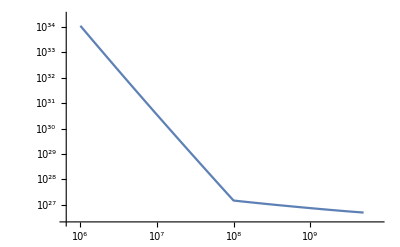

```mathematica
LogLogPlot[Convert[((Mega ElectronVolt)/vesc[WDplot[Log10[ρ]]]^2(trigger[ρ]*Centimeter)^2*ρ*10^-2 Gram/Centimeter^3*1/(12 Giga ElectronVolt)*SpeedOfLight^2(50Kilo Meter))1/(Giga ElectronVolt),d],{ρ,10^6,5*10^9}]
```

#### SN information

```mathematica
eboomreverse[22+Log10[10^-1]]
```

0.768666

```mathematica
snrate=0.3/Century; 
whitedwarfdistribution[m_] := 1/(0.14 Sqrt[2 π])Exp[(-(m - 0.64)^2)/(2 (0.14)^2)];
Qfunction = (FullSimplify[Re[Integrate[whitedwarfdistribution[m], {m,x, 1.456}]]]);
Qcolldecay=Qfunction/.{x->(If[eboomreverse[logmdm+Log10[η]]≥ 0.85, eboomreverse[logmdm+Log10[η]], 0.85])};
```

#### Collision Constraints

```mathematica
σcollision=Γcollision ((ρdm/mdm)^2 (vesc/v)^3 v 4 Pi/3 Rwd^3)^-1;
σobsRX=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
σobsNuStar=Convert[σcollision/.{Γcollision->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Centimeter^2] 1/Centimeter^2;
```

```mathematica
σobsRX/.logmdm->eboom[1.25]
```

3.84821×10^-24

```mathematica
σobsNuStar/.logmdm->eboom[1.25]
```

6.15714×10^-31

```mathematica
integralcollision[logmdm_]:=Re[NIntegrate[vesc[x]^3 4 Pi/3 PJ[x]^3 10^10 whitedwarfdistribution[x],{x,(If[eboomreverse[logmdm]≥ 0.85, eboomreverse[logmdm], 0.85]),1.4}]]
unitlesscollision=Convert[snrate*((10^logmdm Giga ElectronVolt)/(0.4 (Giga ElectronVolt)/Centimeter^3))^2((10^-3 SpeedOfLight)^2)/(SpeedOfLight^3*SolarRadius^3),Centimeter^2] 1/Centimeter^2;
```

```mathematica
unitlesscollision=Convert[snrate*((10^logmdm Giga ElectronVolt)/(0.4 (Giga ElectronVolt)/Centimeter^3))^2((10^-3 SpeedOfLight)^2)/(SpeedOfLight^3*SolarRadius^3),Centimeter^2] 1/Centimeter^2;
```

```mathematica
SNcollision=Plot[Log10[unitlesscollision 1/integralcollision[logmdm]],{logmdm,14.527763646029436,22},PlotStyle->{Purple,Thick}];
```

```mathematica
eboomlimitcollision1=Plot[(100 Sign[x-(eboom[1.25]-Log10[1])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Red}],PlotRange->{-35,-10}];
eboomlimitcollision2=Plot[(100 Sign[x-(eboom[1.25]-Log10[10^-1])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Yellow}],PlotRange->{-35,-10}];
collisionlimitSN=Plot[( 100 Sign[x-14.527763646029436]),{x,14,25},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{-19.907340306203004,5}];
RXcollision=Plot[Log10[σobsRX],{logmdm,eboom[1.25],21},PlotStyle->{Blue,Thick}];
NuStarcollision=Plot[Log10[σobsNuStar],{logmdm,eboom[1.25],21},PlotStyle->{Gray,Thick}];
canvascollision=Plot[-100,{logmdm,14,21},Frame->True,FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "σ_(DM - DM) (cm^2)"},PlotRange->{-35,-10},Axes->None];
```

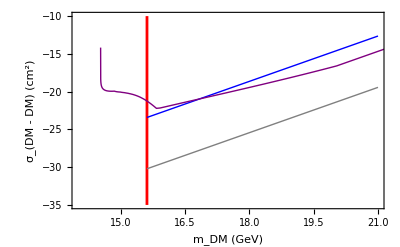

```mathematica
Show[canvascollision,eboomlimitcollision1,RXcollision,NuStarcollision,SNcollision]
```

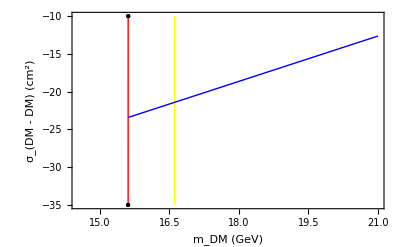

```mathematica
Show[canvascollision,eboomlimitcollision1,eboomlimitcollision2,RXcollision]
```

#### Decay Constraints

```mathematica
integraldecay[logmdm_]:=Re[NIntegrate[vesc[x] 4 Pi/3 Radplot[x]^3 10^10 whitedwarfdistribution[x],{x,(If[eboomreverse[logmdm]≥ 0.85, eboomreverse[logmdm], 0.85]),1.4}]]
unitlessdecay=Convert[1/snrate (0.4(Giga ElectronVolt)/Centimeter^3)/(10^logmdm Giga ElectronVolt)(SpeedOfLight SolarRadius^3)/(10^-3 SpeedOfLight),Giga Year] 1/(Giga Year);
```

```mathematica
SNdecay=Plot[Log10[unitlessdecay integraldecay[logmdm]],{logmdm,14.527763646029436,22},PlotStyle->{Purple,Thick}];
```

```mathematica
Log10[unitlessdecay integraldecay[14.527763646029436]]/.logmdm->14.527763646029436
```

7.26445

```mathematica
τdm=1/Γdecay(ρdm/mdm) (vesc/v)4 Pi/3 Rwd^3;
```

```mathematica
τobsRX=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
τobsNuStar=Convert[τdm/.{Γdecay->1/(5Giga Year),Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->10^3 (Giga ElectronVolt)/Centimeter^3},Giga Year] 1/(Giga Year);
```

```mathematica
τobsRX/.logmdm->eboom[1.25]
```

2.5245×10^12

```mathematica
τobsNuStar/.logmdm->eboom[1.25]
```

6.31125×10^15

```mathematica
RXdecay=Plot[Log10[τobsRX],{logmdm,eboom[1.25],21},PlotStyle->{Blue,Thick}];
NuStardecay=Plot[Log10[τobsNuStar],{logmdm,eboom[1.25],21},PlotStyle->{Gray,Thick}];eboomlimitdecay1=Plot[(100 Sign[x-(eboom[1.25]-Log10[1])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Red}],PlotRange->{5,20}];
eboomlimitdecay2=Plot[(100 Sign[x-(eboom[1.25]-Log10[10^-1])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Yellow}],PlotRange->{5,20}];
decaylimitSN=Plot[(100 Sign[x-14.527763646029436]),{x,14,25},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{-10,7.2644500547759}];
canvasdecay=Plot[-100,{logmdm,14,21},Frame->True,FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "τ_DM (Gyr)"},PlotRange->{5,18},Axes->None];
```

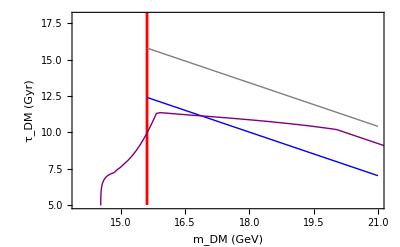

```mathematica
Show[canvasdecay,eboomlimitdecay1,RXdecay,NuStardecay,SNdecay]
```

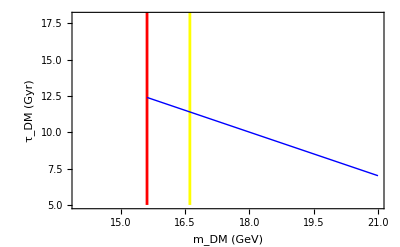

```mathematica
Show[canvasdecay,eboomlimitdecay1,eboomlimitdecay2,RXdecay]
```

```mathematica
Transit Constraints for Subscript[L, 0]<Subscript[λ, T] - ϵ = TeV
```

```mathematica
transitreverse[-16.9]
```

1.39998

```mathematica
transitreverse[-7]
```

0.43768

```mathematica
transitreverse=Interpolation[Table[{Log10[10^-3/ϵ*triggermass[Mwd]^2],Mwd}/.{ϵ->10^3},{Mwd,0.4,1.4,0.01}],InterpolationOrder->1];
integraltransit[logσ_]:=Re[NIntegrate[vesc[x]^2 Pi Radplot[x]^2 10^10 whitedwarfdistribution[x],{x,(If[transitreverse[logσ]≥0.85,transitreverse[logσ], 0.85]),1.40}]]
Qtransit=Qfunction/.{x->If[transitreverse[logσ]≥0.85,transitreverse[logσ], 0.85]};
transitfun=Convert[(ρdm/mdm)π Rwd^2(vesc/v)^2 v/.{Rwd->Radplot[1.25]SolarRadius,vesc->vesc[1.25]SpeedOfLight,mdm->10^logmdm Giga ElectronVolt,v->10^-3 SpeedOfLight,ρdm->0.4 (Giga ElectronVolt)/Centimeter^3},1/Century];
```

```mathematica
unitlesstransit=Convert[1/snrate*0.4 (Giga ElectronVolt)/Centimeter^3*SpeedOfLight^2/(10^-3 SpeedOfLight)*SolarRadius^2,Giga ElectronVolt] 1/(Giga ElectronVolt);
```

```mathematica
Log10[unitlesstransit*integraltransit[-10.94]]
```

46.626

```mathematica
46.62597127249366
```

```mathematica
transitSN=Interpolation[Table[{Log10[unitlesstransit*integraltransit[logσ]],logσ},{logσ,-16.9,-10.94,0.01}]];
```

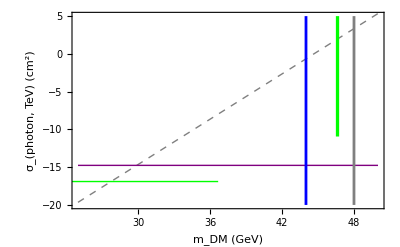

```mathematica
crust=Log10[Convert[vesc[1.25]^2/(10^32 Centimeter^-3*50Kilo Meter)10^mdm/ϵ,Centimeter^2] 1/Centimeter^2];
transitboom=Log10[10^-3/ϵ*triggermass[1.25]^2];
crustplotTeV=Plot[crust/.ϵ->10^3,{mdm,25,50},PlotStyle->{Dashed,Gray,Thick}];
photontransitTeV=Plot[transitboom/.ϵ->10^3,{mdm,25,50},PlotStyle->{Thick,Purple}];
transitSNTeV=Plot[transitSN[logmdm],{logmdm,36.680724877647286,46.62597127249366},PlotStyle->{Green,Thick}];
fluxlimitRX=Plot[( 100 Sign[x-44]),{x,24,50},ExclusionsStyle->Directive[{Thickness[.005],Blue}],PlotRange->{-20,5}];
fluxlimitNuStar=Plot[( 100 Sign[x-48]),{x,24,50},ExclusionsStyle->Directive[{Thickness[.005],Gray}],PlotRange->{-20,5}];
fluxlimitSN=Plot[( 100 Sign[x-46.62597127249366]),{x,24,50},ExclusionsStyle->Directive[{Thickness[.0059],Green}],PlotRange->{-10.94,5}];
tailSN=Plot[-16.9,{x,24,36.680724877647286},PlotStyle->{Green,Thick}];
canvastransit=Plot[-100,{x,25,50},Frame->True,FrameStyle->Black,FrameLabel->{"m_DM (GeV)", "σ_(photon, TeV) (cm^2)"},PlotRange->{-20,5},Axes->None];
crustplotPeV=Plot[crust/.ϵ->10^6,{mdm,25,50},PlotStyle->{Dashed,Gray,Thick}];
photontransitPeV=Plot[transitboom/.ϵ->10^6,{mdm,25,50},PlotStyle->{Thick,Purple}];


Show[canvastransit,crustplotTeV,photontransitTeV,fluxlimitRX,fluxlimitNuStar,fluxlimitSN,tailSN,transitSNTeV]
```

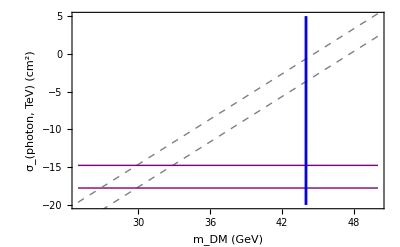

```mathematica
Show[canvastransit,crustplotPeV,photontransitPeV,crustplotTeV,photontransitTeV,fluxlimitRX]
```

#### Q-ball boom

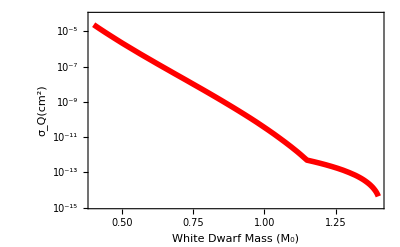

```mathematica
LogPlot[1/10^4*(triggermass[M])^2,{M,0.4,1.4},Frame->True,FrameLabel->{"White Dwarf Mass (M_0)","σ_Q(cm^2)"},FrameStyle->Black,PlotStyle-> {Red,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```

#### Cosmic Ray Constraints

```mathematica
Convert[10^12 SolarMass/(m Giga ElectronVolt/SpeedOfLight^2)*(100 (Kilo Meter)^2)/(30 Kilo Parsec)^2,d]
```

(1.30208×10^35)/m

```mathematica
Convert[(700 1/Century*1/((1.3020802720139689*^35)/10^15))^-1,Giga Year]
```

1.86011×10^10 Giga Year